#### Vectores aleatorios

Escriba aquí los nombres de los integrantes del grupo:
Enrique Pérez Haro
Emilio Gómez Esteban
Fernando Javier López Cerezo
Antonio Trujillo Reino
Alberto Trigueros Postigo

Consideramos la función de densidad conjunta  del vector  dada por

```mathematica
f[x_,y_]:=Piecewise[{{3x,0<y<=x<=1}},0]
f[x,y]
```

Piecewise[{{3 x, 0<y≤x≤1}, {0, True}}]

Buscamos la distribución del vector transformado . Estamos entonces ante un cambio de variable  para la función dada por

```mathematica
g[x_,y_]:={x+y,x-y}
g[x,y]
```

{x+y,x-y}

El teorema de cambio de variable asegura que la densidad del vector  viene dada por  . Debemos primero obtener la inversa

```mathematica
Solve[g[x,y]=={z,w},{x,y}]
```

{{x→(w+z)/2,y→1/2 (-w+z)}}

Podemos definir la función inversa usando el comando anterior, sustituyendo mediante /.

```mathematica
Subscript[g, -1][z_,w_]:={x,y}/.Solve[g[x,y]=={z,w},{x,y}][[1]]
Subscript[g, -1][z,w]
```

{(w+z)/2,1/2 (-w+z)}

Obtenemos la matriz jacobiana derivando cada componente respecto de ambas variables

```mathematica
M=D[Subscript[g, -1][z,w],{{z,w}}]
```

{{1/2,1/2},{1/2,-1/2}}

Y su determinante ( ) es entonces

```mathematica
Subscript[J, Subscript[g, -1]]=Det[M]
```

-1/2

La densidad conjunta del vector  se sigue pues del cambio de variable

```mathematica
Subscript[f, zw][z_,w_]:=Apply[f,Subscript[g, -1][z,w]]Abs[Subscript[J, Subscript[g, -1]]]
Subscript[f, zw][z,w]//Simplify
```

Piecewise[{{(3 (w+z))/4, w<z&&w≥0&&w+z≤2}, {0, True}}]

De la definición anterior obtenemos el soporte del vector  puede escribirse

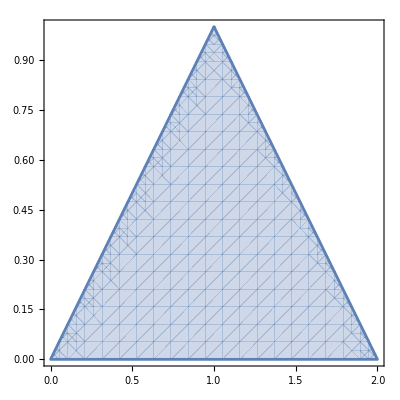

```mathematica
RegionPlot[w<z&&w≥0&&w+z≤2,{z,0,2},{w,0,1}]
```

```mathematica
Integrate[Subscript[f, zw][z,w],{z,0,2},{w,0,1}]
```

1

Calculamos las densidades marginales de  y  integrando la densidad conjunta

```mathematica
Subscript[f, z][z_]:=Integrate[Subscript[f, zw][z,w],{w,0,1}]
Subscript[f, z][z]//Simplify
```

Piecewise[{{(9 z^2)/8, 0<z≤1}, {-3/8 (-4+z^2), 1<z<2}, {0, True}}]

```mathematica
Subscript[f, w][w_]:=Integrate[Subscript[f, zw][z,w],{z,0,2}]
Subscript[f, w][w]//Simplify
```

Piecewise[{{-3/2 (-1+w^2), 0≤w<1}, {0, True}}]

Ambas funciones son densidades (el área bajo las respectivas curvas es 1). Podemos ver sus gráficas

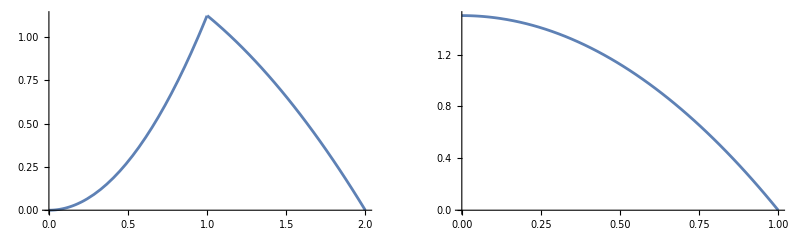

```mathematica
GraphicsRow[{Plot[Evaluate@Subscript[f, z][z],{z,0,2}],Plot[Evaluate@Subscript[f, w][w],{w,0,1}]}]
```

Si queremos calcular, por ejemplo, la esperanza de la variable , usaremos su densidad marginal sabiendo que

```mathematica
Integrate[w Subscript[f, w][w],{w,0,1}]
```

3/8

Obtenemos lo mismo usando la densidad para crear una distribución de probabilidad (objeto de Mathematica)

```mathematica
Subscript[D, w]=ProbabilityDistribution[Subscript[f, w][w],{w,-∞,∞}];
```

```mathematica
Expectation[W,W\[Distributed] Subscript[D, w]]
```

3/8

Podemos entonces realizar otros cálculos, como la probabilidad

```mathematica
Probability[0.3<=W<1,W\[Distributed] Subscript[D, w]]
```

0.5635

También podemos obtener la función generatriz de momentos. Sabemos que su derivada en 0 debe ser la media

```mathematica
Subscript[m, w][t_]:=MomentGeneratingFunction[Subscript[D, w],t]
```

```mathematica
Limit[D[Subscript[m, w][t],t],t->0]
```

3/8

Con respecto al vector , definimos su distribución a partir de su densidad conjunta y calculamos, por ejemplo, el momento de orden

```mathematica
Subscript[D, zw]=ProbabilityDistribution[Subscript[f, zw][z,w],{z,-∞,∞},{w,-∞,∞}];
```

```mathematica
Moment[Subscript[D, zw],{1,2}]
```

5/24

#### Ejercicio: responda a los apartados 2, 3 y 4

Dado un vector aleatorio  con función de densidad conjunta  para  , considere la variable

Halle

Solución: El soporte es el triángulo de vértices  y . Basta entonces

```mathematica
Solve[Integrate[c x(1-y),{x,y}∈Triangle[{{0,0},{1,1},{0,1}}]]==1,c]
```

{{c→24}}

```mathematica
f[x_,y_]:=Piecewise[{{24x(1-y),0<=x<=y<=1}},0]
```

```mathematica
f[x,y]
```

Piecewise[{{24 x (1-y), 0≤x≤y≤1}, {0, True}}]

Use una variable auxiliar  para obtener la densidad de  como marginal de la densidad conjunta de

Buscaremos la distribución del vector (Z,W)=(Y-X,Y)

```mathematica
g[x_,y_]={y-x,y}
```

{-x+y,y}

```mathematica
Solve[g[x,y]=={z,w},{x,y}]
```

{{x→w-z,y→w}}

```mathematica
Subscript[g, -1][z_,w_]:={x,y}/.Solve[g[x,y]=={z,w},{x,y}][[1]]
Subscript[g, -1][z,w]
```

{w-z,w}

```mathematica
M=D[Subscript[g, -1][z,w],{{z,w}}]
```

{{-1,1},{0,1}}

```mathematica
Subscript[J, Subscript[g, -1]]=Det[M]
```

-1

```mathematica
Subscript[f, zw][z_,w_]:=Apply[f,Subscript[g, -1][z,w]]Abs[Subscript[J, Subscript[g, -1]]]
```

```mathematica
Subscript[f, zw][z,w]//Simplify
```

Piecewise[{{-24 (-1+w) (w-z), 0≤w-z≤w≤1}, {0, True}}]

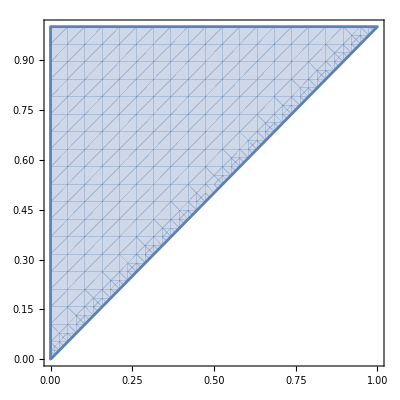

```mathematica
RegionPlot[0≤w-z≤w≤1,{z,0,1},{w,0,1}]
```

```mathematica
Integrate[Subscript[f, zw][z,w],{z,0,1},{w,0,1}]
```

1

```mathematica
Subscript[f, z][z_]:=Integrate[Subscript[f, zw][z,w],{w,0,1}]
Subscript[f, z][z]//Simplify
```

Piecewise[{{-4 (-1+z)^3, 0≤z<1}, {0, True}}]

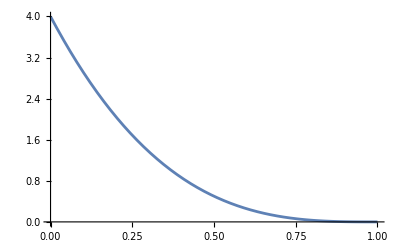

```mathematica
Plot[Evaluate@Subscript[f, z][z],{z,0,1}]
```

Calcule la probabilidad

```mathematica
Dz=ProbabilityDistribution[Subscript[f, z][z],{z,-∞,∞}];
```

```mathematica
Probability[0.3<Z<0.7,Z\[Distributed]Dz]
```

0.232

```mathematica
Integrate[Subscript[f, z][z],{z,0.3,0.7}]
```

0.232

Obtenga la esperanza de

```mathematica
Expectation[Z,Z\[Distributed]Dz]
```

1/5

```mathematica
Integrate[z Subscript[f, z][z],{z,0,1}]
```

1/5